## Set Directories

```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-10-20"}];
dropBoxfolder=FileNameJoin[{"C:","Users","kahrendsen2","Dropbox"}];
dataFolder=FileNameJoin[{"00School","research","DataRuns"}];
folder=FileNameJoin[{dropBoxfolder,dataFolder}];
SetDirectory[folder];
FileNames[]

SetDirectory[FileNameJoin[{folder,"2018-07-10_BalancedPhotoDetectorRound2","data"}]];
(*names=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]];*)
names=FileNames[]
```

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-05-25_LaserProfiling - Shortcut.lnk,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,17-11-18_SystemDiagnosis,17-12-18_SystemDiagnosis,17-12-20_PolarizingElectrons,18-01-03_PolarizingElectrons,18-01-04_PolarizingElectrons,18-01-10_ChamberWarming,18-01-11_SystemDiagnostics,18-01-12_recreatingPolFigure,18-01-13_recreatingPolFigureIncreasedT,18-01-16_morePolarization,18-01-20_electronPolarization,18-01-25_excitationFunctions,18-01-28_bufferGasPressureVsCounts,18-01-28_hayesReproduction,18-02-12_polarizedElectrons,18-02-13,18-02-24_DataFrom18-02-13AllElectronEi100,18-02-27,18-03-01,18-03-02,18-03-03,18-03-06_RubidiumOnWalls,18-03-18_100mTorrBGP,18-03-22_Ei=37eV,18-03-23_pumpScan,18-03-25_springBreakDataReview,18-03-27_770mTorr,18-03-28_PumpPowerScan,18-04-09_PumpLaserRazorProfile,18-04-18,18-05-04,18-05-07,18-06-03,2018-06-07,2018-06-15,2018-06-19_CO2_Data,2018-06-21_ProbeWalkData,2018-06-25_RbProfiles,2018-06-26_SpectrumAnalyzer,2018-06-29_ElectronPolarizationData,2018-07-06_ReorganizingNrbStuff,2018-07-10_BalancedPhotoDetectorRound2,2018-07-10_newAoutToVoltageConversionForHeTarget,dataDump,pumpQWP,README.txt,reallyNiceData,temp,wavemeterOffsets}

{FDayRotation2018-07-11_220134.dat}

## Functions

### Mueller Matrix

#### According to a Chp 22 in an optics handbook (chapter authored by Russell A. Chipman), We have the following mueller matrix for a general retarder

```mathematica
(* The retardance is entered as a fraction. For example, a half-wave plate will be enterered as 1/2 *)
LR[θfast_,retardance_]:=({{1, 0, 0, 0}, {0, Cos[2θfast]^2+Sin[2θfast]^2Cos[2π retardance], Sin[2θfast]Cos[2θfast](1-Cos[2π retardance]), -Sin[2θfast]Sin[2π retardance]}, {0, Sin[2θfast]Cos[2θfast](1-Cos[2π retardance]), Sin[2θfast]^2+Cos[2θfast]Cos[2π retardance]^2, Cos[2 θfast]Sin[2π retardance]}, {0, Sin[2θfast]Sin[2π retardance], -Cos[2 θfast]Sin[2π retardance], Cos[2π retardance]}})
LRzero[δ_]:=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Cos[δ], Sin[δ]}, {0, 0, -Sin[δ], Cos[δ]}});
LPzero=1/2({{1, 1, 0, 0}, {1, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
MuellerRotation[θ_]:=({{1, 0, 0, 0}, {0, Cos[2θ], -Sin[2θ], 0}, {0, Sin[2θ], Cos[2θ], 0}, {0, 0, 0, 1}})
```

### Discreet Fourier Transform

```mathematica
(* Discreet Fourier Transform for the Cos Function *)
```

```mathematica
DFTC[list_,rev_]:=Module[{numItems,i,k,j,returnList,intensity},
returnList={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnList,0];
];

For[k=1,k<=numItems,k++,
intensity=list[[k]];
For [i=0,i<numItems/2,i++,
If[i==0 ||i==(numItems/2-1),
returnList[[i+1]]=returnList[[i+1]]+1/numItems*intensity*Cos[2*π *i *rev* (k-1)/numItems];,
returnList[[i+1]]=returnList[[i+1]]+2/numItems*intensity*Cos[2*π *i* rev *(k-1)/numItems];
];
];
];

returnList
];
(* Discreet Fourier Transform for the Sin Function *)
DFTS[list_,rev_]:=Module[{numItems,i,k,j,error,returnList,intensity,errors},
returnList={};
error={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnList,0];
AppendTo[errors,0];
];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnList[[k+1]]=returnList[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems];,
returnList[[k+1]]=returnList[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems];
];
];
];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnList[[k+1]]=returnList[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems];,
returnList[[k+1]]=returnList[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems];
];
];
];

returnList
];
DFT[list_,rev_]:={DFTS[list,rev],DFTC[list,rev]};
```

### Other Functions

```mathematica
Needs["ErrorBarPlots`"]
GenerateListOfFileNames[prefix_,date_,runtimes_]:=Module[{j,fileNames},
fileNames={};
For[j=1,j≤Length[runtimes],j++,
AppendTo[fileNames,StringJoin[prefix,date,"_",ToString[runtimes[[j]]],".dat"]]
];
fileNames
];
(*ErrorListPlot2 is a convenience function. It accepts as an argument a list of lists. The first level of lists can have any length. The second level should have 3 elements. The first element is the independent variable, the second element is the dependent variable, and the third element is the error associated with the depenedent variable.*)
ErrorListPlot2[data_]:=Module[
{orderedPairs,dataT,errorValues,errorBars,errorBarData,i},
dataT=Transpose[data];
orderedPairs=Transpose[Drop[dataT,-1]];
errorValues=Drop[dataT,{1,2}];
errorBars=ErrorBar[errorValues][[1]];
errorBarData={};
For[i=1,i≤Length[data],i++,
AppendTo[errorBarData,{orderedPairs[[i]],ErrorBar[errorValues[[1]][[i]]]}];
];
ErrorListPlot[errorBarData]
];
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k,rawImport,removedNulls,joinedWithSpaces},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
rawImport=Take[rawFile[[k]],{2,-1}];
removedNulls=DeleteCases[rawImport,Null];
joinedWithSpaces=StringRiffle[removedNulls];
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"-> "",":"->""}]->joinedWithSpaces];
,
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"->"",":"->""}]->rawFile[[k]][[2]]];
];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];
headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
ImportFile[dataFileName_]:={GetFileHeaderInfo[dataFileName],GetFileDataset[dataFileName]}
```

## Import Data for analysis

```mathematica
(* Imports the file and separates the header information from the dataset. 
    The data is stored as a list. 
	The first element in the list is an association which has all of the 
header info.
	the second element in the list has the dataset.*)
data=ImportFile[names[[1]]];
data[[1]];
dataset=data[[2]];
(* The angular position is recorded in steps, modify it to be recorded in radians *)
datasetRad=dataset[All,{#["STEP"] *2π/350&,"PMP"}];
(* Typically it's best to work with lists, the most simple form of array, so we convert the structured datasetRad to the "Normal" list. *)
datasetNormal=Normal[datasetRad]
```

{{0,0.21388},{π/25,0.121443},{(2 π)/25,0.045341},{(3 π)/25,0.003817},{(4 π)/25,0.006335},{π/5,0.054882},{(6 π)/25,0.136633},{(7 π)/25,0.229833},{(8 π)/25,0.312271},{(9 π)/25,0.364329},{(2 π)/5,0.371504},{(11 π)/25,0.333873},{(12 π)/25,0.259144},{(13 π)/25,0.165868},{(14 π)/25,0.079308},{(3 π)/5,0.018472},{(16 π)/25,0.000229},{(17 π)/25,0.02725},{(18 π)/25,0.094116},{(19 π)/25,0.183042},{(4 π)/5,0.2738},{(21 π)/25,0.343338},{(22 π)/25,0.374405},{(23 π)/25,0.358528},{(24 π)/25,0.298913},{π,0.212124},{(26 π)/25,0.120603},{(27 π)/25,0.044272},{(28 π)/25,0.003893},{(29 π)/25,0.007251},{(6 π)/5,0.056256},{(31 π)/25,0.136862},{(32 π)/25,0.230673},{(33 π)/25,0.312729},{(34 π)/25,0.365245},{(7 π)/5,0.372496},{(36 π)/25,0.334789},{(37 π)/25,0.258992},{(38 π)/25,0.165486},{(39 π)/25,0.080224},{(8 π)/5,0.019464},{(41 π)/25,0.000687},{(42 π)/25,0.02664},{(43 π)/25,0.093582},{(44 π)/25,0.182966},{(9 π)/5,0.273571},{(46 π)/25,0.343948},{(47 π)/25,0.375931},{(48 π)/25,0.357306},{(49 π)/25,0.299905}}

## First, we pass the 45° light through a horizontal linear polarizer and a vertical linear polarizer.

#### We will assume our incident vector is 100% linearly polarized in the horizontal direction

```mathematica
inc=({{1}, {1}, {0}, {0}})
```

{{1},{1},{0},{0}}

### First Horizontal

```mathematica
LPzero.inc
```

{{1},{1},{0},{0}}

### Then vertical

```mathematica
vertLP=MuellerRotation[π/2].LPzero.Transpose[MuellerRotation[π/2]];
vertLP.inc
```

{{0},{0},{0},{0}}

### The light disappears as expected.

### Now we start with horizontally polarized input.

```mathematica
inc=({{1}, {1}, {0}, {0}})
```

{{1},{1},{0},{0}}

### Then we rotate it to our desired starting angle.

```mathematica
arbInc[θo_]:=MuellerRotation[θo].inc
```

```mathematica
arbInc[π/2]
```

{{1},{-1},{0},{0}}

### We then put it through a rotatable linear polarizer.

1/2+1/2 Cos[2 θ] Sin[2 θ]+1/4 √3 (Cos[2 θ]^2-Sin[2 θ]^2)

1/2-1/2 Cos[2 θ] Sin[2 θ]+1/4 √3 (-Cos[2 θ]^2+Sin[2 θ]^2)

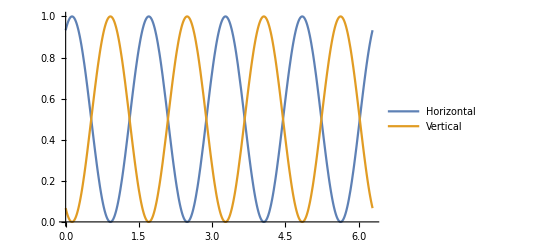

{{0,1,0,0},{1,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Clear[arbLP]
arbLP[θ_]:=MuellerRotation[θ].LPzero.Transpose[MuellerRotation[θ]];
incidenceAngle=15*π/180;
horizontalResult=(arbLP[0].LR[θ,1/2].arbInc[incidenceAngle])[[1]][[1]]
verticalResult=(arbLP[π/2].LR[θ,1/2].arbInc[incidenceAngle])[[1]][[1]]

Plot[{horizontalResult,verticalResult},{θ,0,2π},PlotLegends->{"Horizontal","Vertical"}]
balancedIntensity=(LPzero.arbinc)[[1]]-(vertLP.arbinc)[[1]]
```

```mathematica
horizontalModel[ang,ret,th0,A]
```

{{A (1/2+1/2 (1-Cos[2 π ret]) Cos[2 (ang+th0)] Sin[2 th0] Sin[2 (ang+th0)]+1/2 Cos[2 th0] (Cos[2 (ang+th0)]^2+Cos[2 π ret] Sin[2 (ang+th0)]^2))},{A (1/2+1/2 (1-Cos[2 π ret]) Cos[2 (ang+th0)] Sin[2 th0] Sin[2 (ang+th0)]+1/2 Cos[2 th0] (Cos[2 (ang+th0)]^2+Cos[2 π ret] Sin[2 (ang+th0)]^2))},{0},{0}}

## First We fit the model to get an approximation of the retardance

```mathematica
horizontalModel[θ_,ret_,θo_,A_]:=A*(arbLP[0].LR[θ+θo,ret].arbInc[θo]);
verticalModel[θ_,ret_,θo_,A_]:=A*(arbLP[π/2].LR[θ+θo,ret].arbInc[θo]);
fit=NonlinearModelFit[datasetNormal,{(horizontalModel[ang,ret,th0,A])[[1]][[1]],ret< 2},{th0,{ret,.5},A},ang]
```

FittedModel[0.374319 (1/2+0.989676 Cos[2 (0.713488+ang)] Sin[2 (0.713488+ang)]+0.071663 (Cos[2 (0.713488+ang)]^2-1. Sin[2 (0.713488+ang)]^2))]

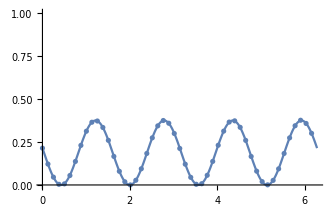

0.499999

40.8798

0.499999

{th0→0.713488,ret→0.499999,A→0.374319}

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{0.000448423,38.9935,0.000211844}

```mathematica
plotRange={{0,2π},{0,1}};
rawDataPlot=ListPlot[datasetNormal];
modelFitPlot =Plot[fit[θ],{θ,0,2π}];
Show[{rawDataPlot,modelFitPlot},PlotRange->plotRange]
ret/.fit["BestFitParameters"]
(th0/.fit["BestFitParameters"])*180/π
actualPlateRetardance=Mod[ret/.fit["BestFitParameters"],2]
fit["BestFitParameters"]
fit["ParameterErrors"]
```

```mathematica
Mod[38.9935,2]/2
```

0.49675

## With the retardance estimate obtained, we lock in the value of the retardance and find the initial angle (th0)

```mathematica
fit2=NonlinearModelFit[datasetNormal,(horizontalModel[ang,ret/.fit["BestFitParameters"],th0,A])[[1]][[1]],{th0,A},ang];
fit2BFP=fit2["BestFitParameters"]
(th0/.fit2BFP )*180/π
```

{th0→0.713488,A→0.374319}

40.8798

## With the starting angle obtained, we now fit to find the retardance more precisely

```mathematica
fit3=NonlinearModelFit[datasetNormal,{(horizontalModel[ang,ret,th0,A])[[1]][[1]],0<ret<2},{th0,{ret,.5},A},ang];
fit3BFP=fit3["BestFitParameters"]
(ret/.fit3BFP )
fit3["ParameterErrors"]
```

{th0→0.713488,ret→0.500003,A→0.374319}

0.500003

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{0.000448423,19.4493,0.000211844}